```mathematica
P=9x-6y+4x y-5 x^2;
Q=6x-6 y-5x y+4 y^2;Solve[{P==0,Q==0},{x,y}]
```

{{x→0,y→0},{x→1,y→2},{x→2,y→1}}

```mathematica
P=9x-6y+4x y-5 x^2;
Q=6x-6 y-5x y+4 y^2;J=({{D[P,x], D[P,y]}, {D[Q,x], D[Q,y]}})
```

{{9-10 x+4 y,-6+4 x},{6-5 y,-6-5 x+8 y}}

```mathematica
ID=IdentityMatrix[2];
x=0;y=0;
Solve[Det[J-λ ID]==0,λ ]
```

{{1,0},{0,1}}

{{λ→-3},{λ→6}}

```mathematica
P=9x-6y+4x y-5 x^2;
Q=6x-6 y-5x y+4 y^2;J=({{D[P,x], D[P,y]}, {D[Q,x], D[Q,y]}});
ID=IdentityMatrix[2];
x=1;y=2;
Solve[Det[J-λ ID]==0,λ ]
```

{{λ→3},{λ→9}}

```mathematica
P=9x-6y+4x y-5 x^2;
Q=6x-6 y-5x y+4 y^2;J=({{D[P,x], D[P,y]}, {D[Q,x], D[Q,y]}});
ID=IdentityMatrix[2];
x=2;y=1;
Solve[Det[J-λ ID]==0,λ ]
```

{{λ→-9},{λ→-6}}

```mathematica
P=9x-6y+4x y-5 x^2;
Q=6x-6 y-5x y+4 y^2;
y=k x+b;
Collect[k P-Q,x]
```

6 b-4 b^2-6 b k+(-6+5 b+15 k-4 b k-6 k^2) x

```mathematica
Solve[{-6+5 b+15 k-4 b k-6 k^2==0,6 b-4 b^2-6 b k==0},{k,b}]
```

{{b→0,k→1/2},{b→0,k→2},{b→3,k→-1}}

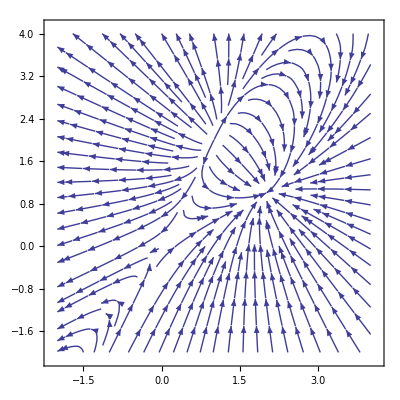

```mathematica
P=9x-6y+4x y-5 x^2;
Q=6x-6 y-5x y+4 y^2;
StreamPlot[{P,Q},{x,-2,4},{y,-2,4},Axes->True]
```

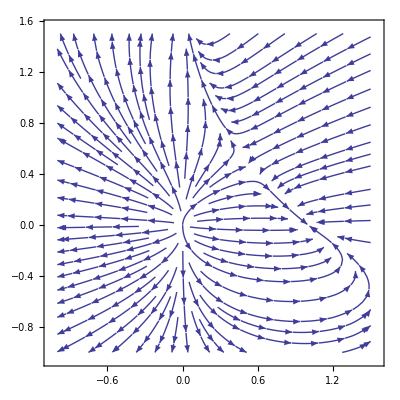

```mathematica
P=x(1-x-y);
Q=(y(2-3x-y))/4;
StreamPlot[{P,Q},{x,-1,1.5},{y,-1,1.5},Axes->True]
```